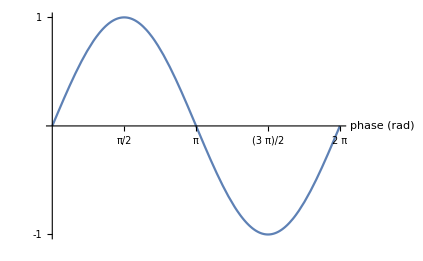

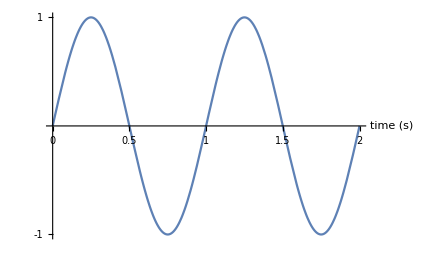

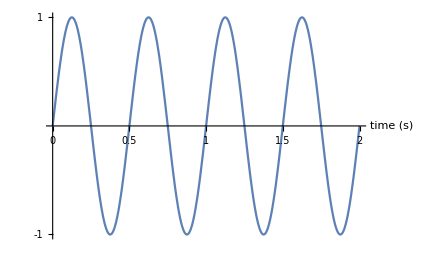

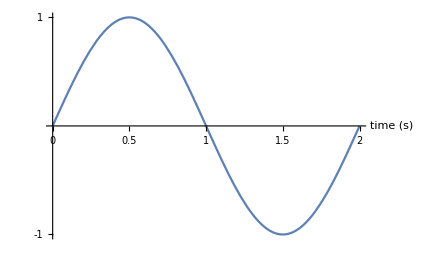

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"phase (rad)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[4π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[1π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
```

```mathematica
6.43*10^-4*80^2
```

4.1152

Lesson 2

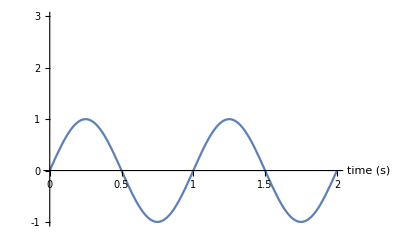

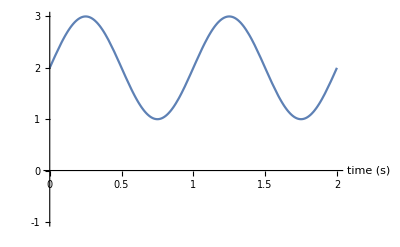

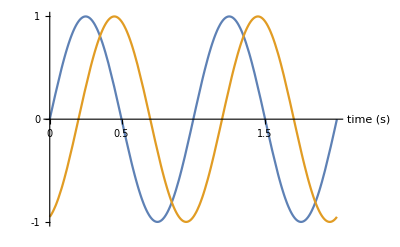

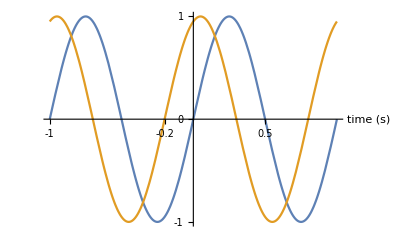

```mathematica
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,0,1,2,3}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,3}]
Plot[2+Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,0,1,2,3}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,3}]
Plot[{Sin[2π t],Sin[2π (t-0.2)]},{t,0,2},Ticks->{{0,0.2,0.5,1,1.5,2},{-1,0,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,1}]
Plot[{Sin[2π t],Sin[2π (t+0.2)]},{t,-1,1},Ticks->{{-1,-0.5,-0.2,0,0.5,1,1.5,2},{-1,0,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,1}]
```

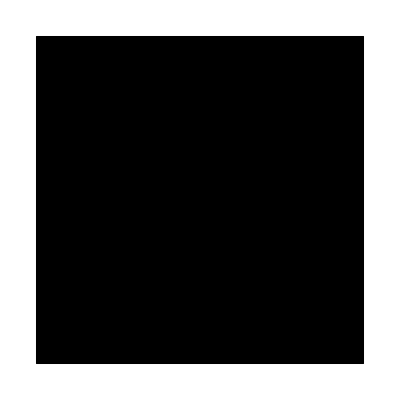

```mathematica
Graphics[{EdgeForm[{Thick, Black}],Rectangle[]}]
```

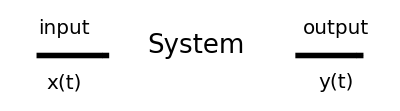

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["input",FontSize->20],{-5,8}],
Text[Style["x(t)",FontSize->20],{-5,2}],
Text[Style["output",FontSize->20],{25,8}],
Text[Style["y(t)",FontSize->20],{25,2}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
```

```mathematica
Graphics[{Style[Line[{{0,2},{0,-5}}], Thick,Dashed],
Line[{{0,0},{3,-3}}],
Circle[{0,0},1,{-π/2,-.8}],
Text[Style["y",FontSize->23],{0.5,-1.5}],
Disk[{3,-3},0.3]
}]
```

-Graphics-

```mathematica
Simplify[Sin[a]/Sin[b]]
```

Csc[b] Sin[a]

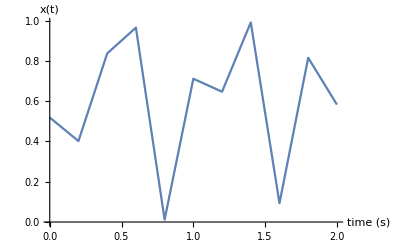

```mathematica
ListPlot[Table[{n,RandomReal[]},{n,0,2,0.2}],Joined->True,AxesLabel->{"time (s)","x(t)"},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
```

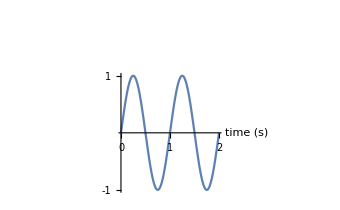

```mathematica
sinPlot=Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]];
Show[{Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]],
Graphics[{
Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["input",FontSize->20],{-5,8}],
Text[Style["x(t)",FontSize->20],{-5,2}],
Text[Style["output",FontSize->20],{25,8}],
Text[Style["y(t)",FontSize->20],{25,2}],
Text[Style["System",FontSize->26],{9.5,6}]
}]}]
```

```mathematica
1^2/2^2
```

1/4

```mathematica
1/(1-1/3)
```

3/2

```mathematica
1/(1-1/4.)
1/(1-4/1.)
```

1.33333

-0.333333

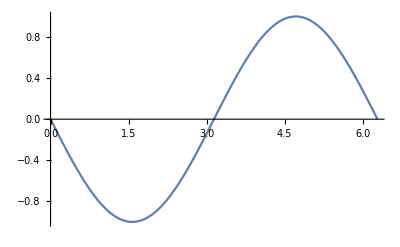

```mathematica
Plot[Sin[x-π],{x,0,2π}]
```

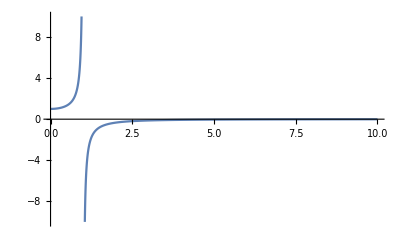

```mathematica
Plot[1/(1-w^2),{w,0,10},PlotRange->{-10,10}]
```

```mathematica
1/(1-1/9.)*0.2
```

0.225

```mathematica
Solve[1/(1-4/1.)*x==1]
```

{{x→-3.}}

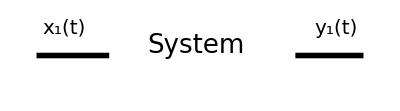

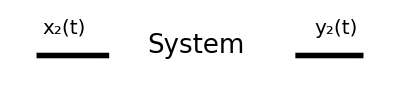

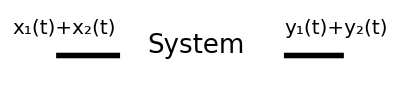

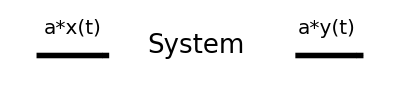

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["x_1(t)",FontSize->20],{-5,8}],
Text[Style["y_1(t)",FontSize->20],{25,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["x_2(t)",FontSize->20],{-5,8}],
Text[Style["y_2(t)",FontSize->20],{25,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["x_1(t)+x_2(t)",FontSize->20],{-7,8}],
Text[Style["y_1(t)+y_2(t)",FontSize->20],{27,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["a*x(t)",FontSize->20],{-4,8}],
Text[Style["a*y(t)",FontSize->20],{24,8}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
```

```mathematica
ω1=2;
ω2=0.5;
1/(1-ω1^2)*(-3)
1/(1-ω2^2)*0.75
```

1

1.

```mathematica
∑_j Subscript[A, jr] Subscript[A, js]
```

```mathematica
∫_0^(2π) Sin[ϕ]^2 ⅆϕ
```

π

```mathematica
∫_0^(2π) Sin[ϕ]Cos[ϕ]ⅆϕ
```

0

```mathematica
∫_(-π/2)^(π/2) Cos[θ]ⅆθ
```

2

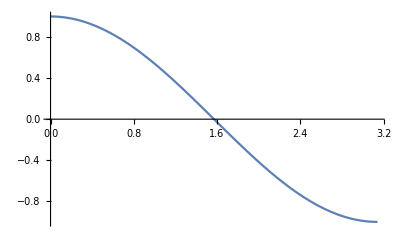

```mathematica
Plot[Cos[θ],{θ,0,π}]
```

```mathematica
∫_0^(2π) Sin[ϕ]^2 ⅆϕ
```

π

```mathematica
∫_0^(2π) Sin[ϕ]*Cos[ϕ]ⅆϕ
```

0

```mathematica
Eigensystem[({{2, 0, 0}, {0, 2, 0}, {0, 0, 4}})]
Eigenvalues[({{2, 0, 0}, {0, 2, 0}, {0, 0, 2}})]
```

{{4,2,2},{{0,0,1},{0,1,0},{1,0,0}}}

{2,2,2}

```mathematica
Sin[60°]*Cos[60°]
```

(√3)/4

```mathematica
(5*√3)/8.
```

1.08253

```mathematica
UnitConvert[12/(20*1.08*10^-8)hr,yr]
```

6341.96 yr

```mathematica
Unprotect[q]
Clear[q]
```

{q}

```mathematica
q[Q_,P_]:=√(2*P)Sin[Q]
p[Q_,P_]:=√(2*P)Cos[Q]
```

```mathematica
D[q[Q,P], Q]
D[q[Q,P], P]
```

√2 √P Cos[Q]

Sin[Q]/(√2 √P)

```mathematica
1/Cos[40°]*12.
```

15.6649

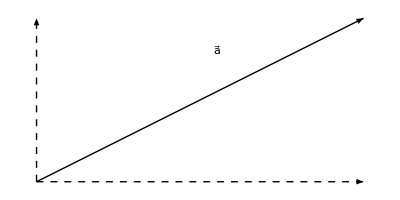

```mathematica
Graphics[
{
Arrow[{{0,0},{2,1}}],
Style[Arrow[{{0,0},{2,0}}],Dashed],
Style[Arrow[{{0,0},{0,1}}],Dashed],
Style[Text["a⃗",{1.1,0.8}],FontSize->25]

}
]
```

```mathematica
OverVector[a]
```

a⃗

```mathematica
P
```

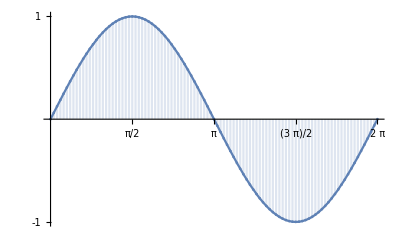

```mathematica
Show[plots={Plot[Sin[x],{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16]]
,DiscretePlot[Sin[x],{x,0,2π,(2π)/100.}]}]
```

```mathematica
vector=Rasterize[MatrixForm[Append[Table[Round[Sin[x]//N,0.01],{x,0,(2π)/10.,(2π)/100}],"..."]]]
```

-Graphics-

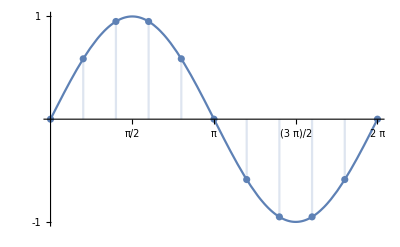

```mathematica
plots=Show[plots]
```

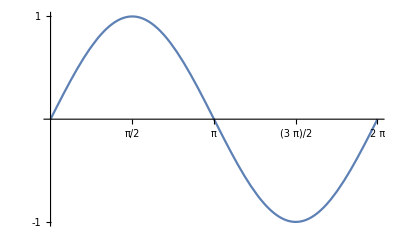

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16]]
```

```mathematica
Append[{a},b]
```

{a,b}

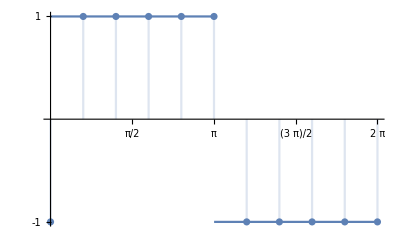

-Graphics-

```mathematica
Show[plots={Plot[SquareWave[x/(2π)],{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16]]
,DiscretePlot[SquareWave[x/(2π)-0.001],{x,0,2π,(2π)/10.}]}]
vector=Rasterize[MatrixForm[Table[Round[SquareWave[x/(2π)]//N,0.01],{x,0,2π,(2π)/10}]]]
```

```mathematica
squareVector=Table[SquareWave[x/(2π)]//N,{x,0,2π,π/5.}];
sineVector=Table[Sin[x],{x,0,2π,π/5.}];
```

```mathematica
sineVector.squareVector*π/5
```

3.86753

```mathematica
∫_0^(2π) Sin[x]*SquareWave[x/(2π)]ⅆx
```

4

```mathematica
∫_0^(2π) Sin[x]^2 ⅆx
```

π

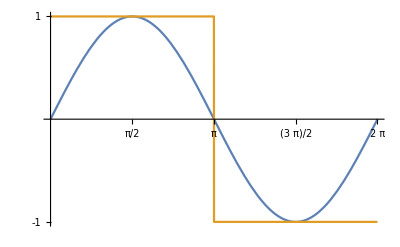

```mathematica
Plot[{Sin[x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

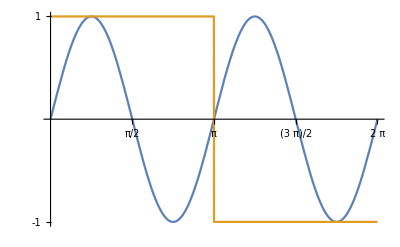

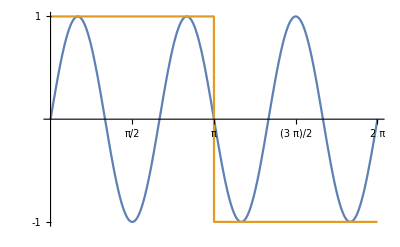

```mathematica
Plot[{Sin[2x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{Sin[3x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
∫_0^(2π) Sin[x]Sin[2x]ⅆx
```

0

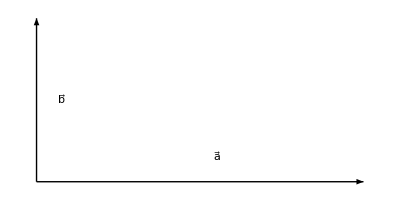

```mathematica
Graphics[
{
Style[Arrow[{{0,0},{2,0}}]],
Style[Arrow[{{0,0},{0,1}}]],
Style[Text["a⃗",{1.1,0.15}],FontSize->25],
Style[Text["b⃗",{0.15,0.5}],FontSize->25]

}
]
```

```mathematica
OverVector[b]
```

b⃗

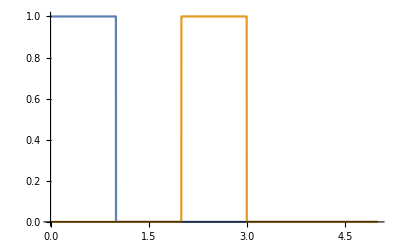

```mathematica
Plot[{UnitStep[t]-UnitStep[t-1],UnitStep[t-2]-UnitStep[t-3]},{t,0,5},Exclusions->None]
```

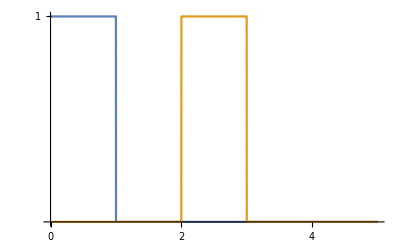

```mathematica
Show[plots={Plot[{UnitStep[t]-UnitStep[t-1],UnitStep[t-2]-UnitStep[t-3]},{t,0,5},Ticks->{{0,1,2,3,4,5},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
}]
```

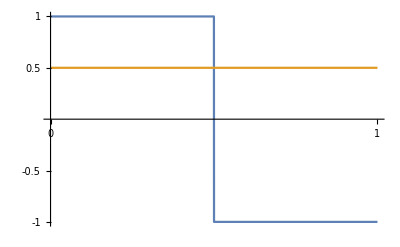

```mathematica
Show[plots={Plot[{SquareWave[t],0.5},{t,0,1},Ticks->{{0,0.5,1,2,3,4,5},{-1,-0.5,0.5,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
}]
```

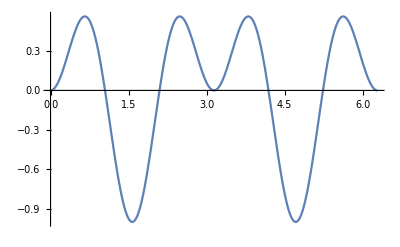

```mathematica
Plot[Sin[x]*Sin[3x],{x,0,2π}]
```

```mathematica
∫_0^(2π) Sin[x]*Sin[x]ⅆx
```

π

```mathematica
1/π∫_0^(2π) SquareWave[x/(2π)]*Sin[n*x]ⅆx//Simplify
```

(1-2 Cos[n π]+Cos[2 n π])/(n π)

```mathematica
(1-2 Cos[n π]+Cos[2 n π])/n
```

```mathematica
b[1]
```

4/π

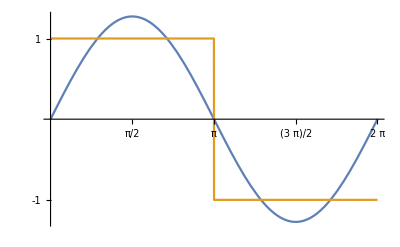

```mathematica
Plot[{Sin[x]*4/π,SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

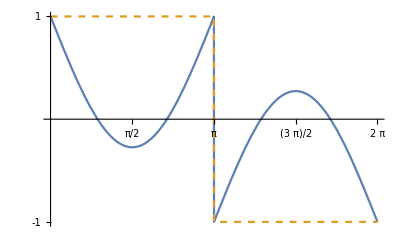

Plot::nonopt: Options expected (instead of Null) beyond position 2 in Plot[{(-(Sin[x] 4)/π+SquareWave[x/Times[«2»]])^2},{x,0,2 π},Ticks→{{π/2,π,(3 π)/2,2 π},{-1,1}},TicksStyle→Directive[Label,14],AxesLabel→{None,None},AxesStyle→Directive[Label,16],Exclusions→None,Null]. An option must be a rule or a list of rules.

Plot[{(-(Sin[x] 4)/π+SquareWave[x/(2 π)])^2},{x,0,2 π},Ticks→{{π/2,π,(3 π)/2,2 π},{-1,1}},TicksStyle→Directive[Label,14],AxesLabel→{None,None},AxesStyle→Directive[Label,16],Exclusions→None,Null]

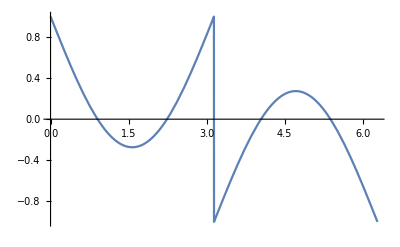

```mathematica
Plot[{-Sin[x]*4/π+SquareWave[x/(2π)],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotStyle->{Automatic,Dashed}]
Plot[{(-Sin[x]*4/π+SquareWave[x/(2π)])^2},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,]
```

```mathematica
∫_0^(2π) (SquareWave[x/(2π)]-f1[x])^2 ⅆx//N
∫_0^(2π) (SquareWave[x/(2π)]-f1[x]*0.99)^2 ⅆx//N
```

1.19023

1.19074

```mathematica
∫_0^(2π) Sin[n*x]^2 ⅆx
∫_0^(2π) SquareWave[x/(2π)]^2 ⅆx
```

π-Sin[4 n π]/(4 n)

2 π

```mathematica
Sin[x]
```

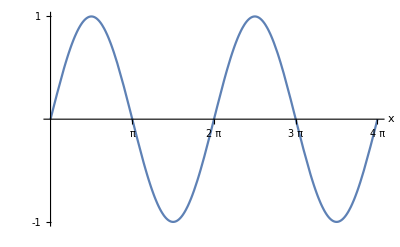

```mathematica
Plot[Sin[x],{x,0,4π},Ticks->{{π,2π,3π,4π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"x", None},AxesStyle->Directive["Label", 16]]
```

```mathematica
2/(8π)∫_0^(8π) Sin[x]^2 ⅆx//N
```

1.

```mathematica
∫_0^(2π) Sin[x]^2 ⅆx
```

π

```mathematica
1/π∫_0^(2π) SquareWave[x/(2π)]*Sin[n*x]ⅆx
```

(1-2 Cos[n π]+Cos[2 n π])/(n π)

```mathematica
b[5]
```

4/(5 π)

```mathematica
∫_0^(2π) (SquareWave[x/(2π)]-f20[x])^2 ⅆx
```

```mathematica
(2 (-38908018390082189908109307104+3982549742588656443243414375 π^2))/(3982549742588656443243414375 π)//N
```

0.0636487

```mathematica
f20[x]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)+(4 Sin[11 x])/(11 π)+(4 Sin[13 x])/(13 π)+(4 Sin[15 x])/(15 π)+(4 Sin[17 x])/(17 π)+(4 Sin[19 x])/(19 π)+(4 Sin[21 x])/(21 π)+(4 Sin[23 x])/(23 π)+(4 Sin[25 x])/(25 π)+(4 Sin[27 x])/(27 π)+(4 Sin[29 x])/(29 π)+(4 Sin[31 x])/(31 π)+(4 Sin[33 x])/(33 π)+(4 Sin[35 x])/(35 π)+(4 Sin[37 x])/(37 π)+(4 Sin[39 x])/(39 π)

```mathematica
b[n_]:=1/π Limit[2/n0*(1-Cos[n0*π]),n0->n]
f[nmax_,x_]:=∑_(n=0)^nmax b[n]*Sin[n x]
f1[x_]=f[1,x];
f3[x_]=f[3,x];
f5[x_]=f[5,x];
f25[x_]=f[25,x];
f200[x_]=f[200,x];
```

-Graphics-

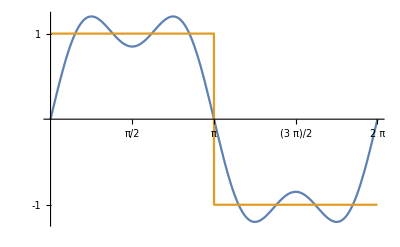

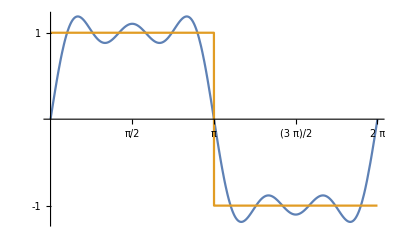

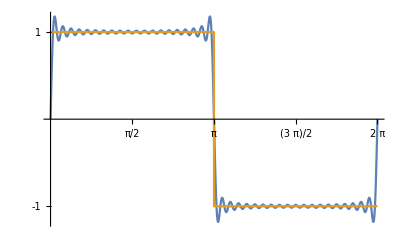

```mathematica
Plot[{f1[x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{f2[x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{f5[x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{f20[x],SquareWave[x/(2π)]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

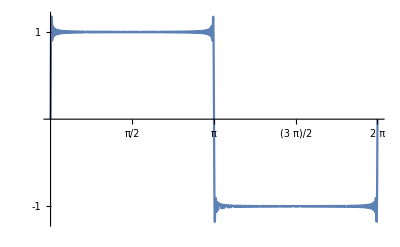

```mathematica
Plot[{f200[x]},{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

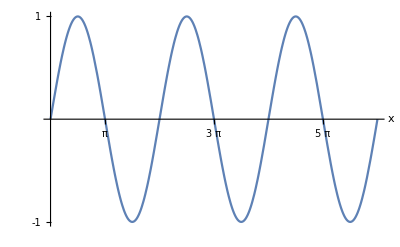

```mathematica
Plot[Sin[x],{x,0,6π},Ticks->{{π,2π,3π,4π,5π,6π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"x", None},AxesStyle->Directive["Label", 16]]
```

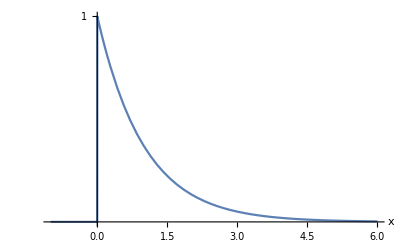

```mathematica
Plot[ⅇ^-x*UnitStep[x],{x,-1,6},Ticks->{{},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"x", None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->Full]
```

```mathematica
∫_0^∞ (ⅇ^-x)^2 ⅆx
```

1/2

```mathematica
1/(2π)∫_0^(2π) Sin[x]^2 ⅆx
```

1/2

```mathematica
1/(2π)∫_0^(2π) (SquareWave[x/(2π)]-Sin[x])^2 ⅆx//N
```

0.22676

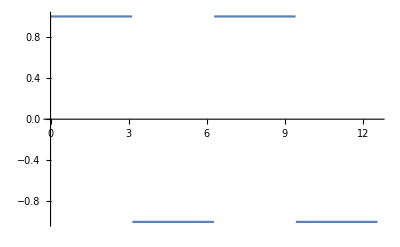

```mathematica
Plot[SquareWave[x/(2π)],{x,0,4π}]
```

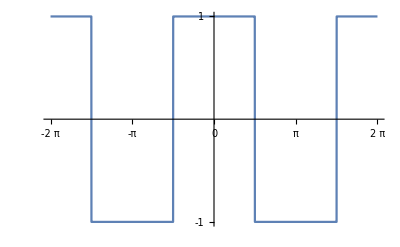

```mathematica
Plot[SquareWave[(x+π/2)/(2π)],{x,-2π,2π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
b2[n_]=Simplify[∫_0^(2π) SquareWave[(x+π/2)/(2π)]*Sin[n*x]ⅆx,Assumptions->n∈Integers]
```

-(64 Cos[(n π)/4]^2 Cos[(n π)/2] Sin[(n π)/4]^4)/n

```mathematica
b2[7]
```

0

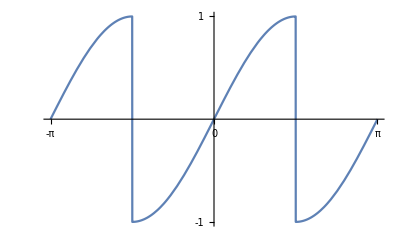

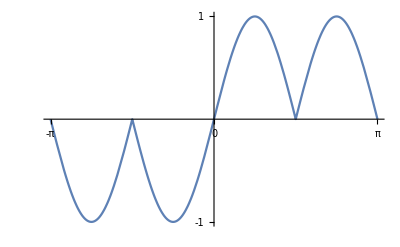

```mathematica
Plot[SquareWave[(x+π/2)/(2π)]*Sin[x],{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[SquareWave[(x+π/2)/(2π)]*Sin[2x],{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

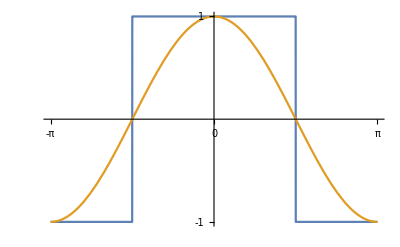

```mathematica
Plot[{SquareWave[(x+π/2)/(2π)],Cos[x]},{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
a[n_]=Simplify[1/π∫_-π^π SquareWave[(x+π/2)/(2π)]*Cos[n*x]ⅆx,Assumptions->n∈Integers]
b[n_]=Simplify[1/π∫_-π^π SquareWave[x/(2π)]*Sin[n*x]ⅆx,Assumptions->n∈Integers]
```

(4 Sin[(n π)/2])/(n π)

-(2 (-1+(-1)^n))/(n π)

```mathematica
a[1]
b[1]
```

4/π

4/π

```mathematica
test[n_]=(4*Sin[(n π)/2])/(n π)-(2/(n π))*(1-Cos[n π])
```

-(2 (1-Cos[n π]))/(n π)+(4 Sin[(n π)/2])/(n π)

```mathematica
Table[a[n],{n,1,10}]
Table[b[n],{n,1,10}]
```

{4/π,0,-4/(3 π),0,4/(5 π),0,-4/(7 π),0,4/(9 π),0}

{4/π,0,4/(3 π),0,4/(5 π),0,4/(7 π),0,4/(9 π),0}

```mathematica
g[n_,x_]:=∑_(i=1)^n a[i]*Cos[i*x]
```

```mathematica
g1[x_]=g[1,x];
g3[x_]=g[5,x];
g5[x_]=g[5,x];
g25[x_]=g[25,x];
g200[x_]=g[200,x];
```

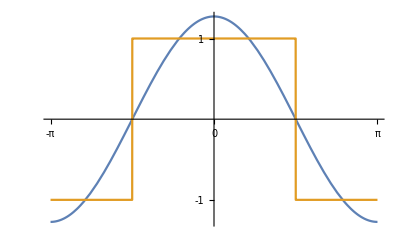

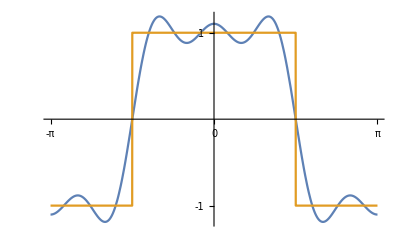

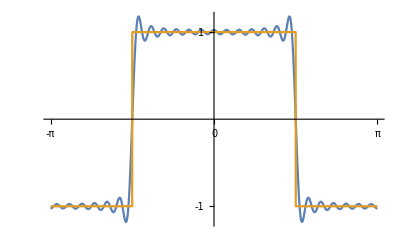

```mathematica
Plot[{g1[x],SquareWave[(x+π/2)/(2π)]},{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{g3[x],SquareWave[(x+π/2)/(2π)]},{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{g25[x],SquareWave[(x+π/2)/(2π)]},{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{g200[x],SquareWave[(x+π/2)/(2π)]},{x,-π,π},Ticks->{{-2π,-π,0,π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

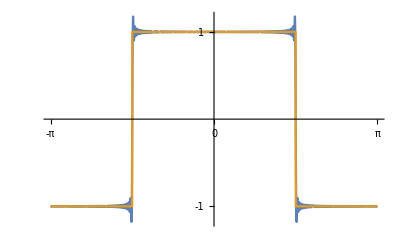
```mathematica
tm&[-Graphics-
```

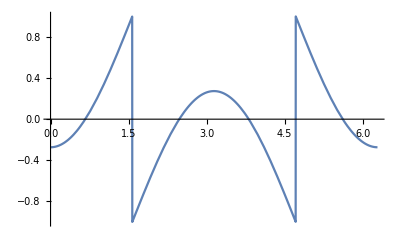

-Graphics-

```mathematica
Plot[SquareWave[(x+π/2)/(2π)]-g1[x],{x,0,2π},Exclusions->None]
Plot[SquareWave[x/(2π)]-4/π Sin[x],{x,0,2π},Exclusions->None]
```

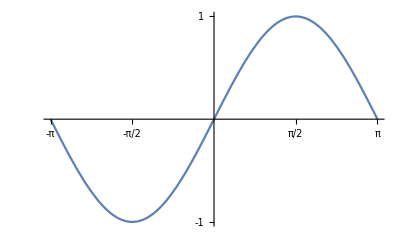

```mathematica
Plot[{Sin[x]},{x,-π,π},Ticks->{{-π,-π/2,π/2,π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

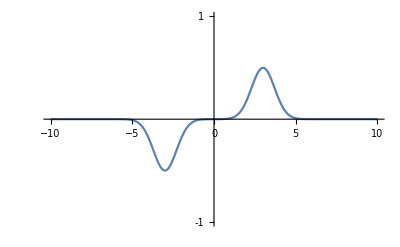

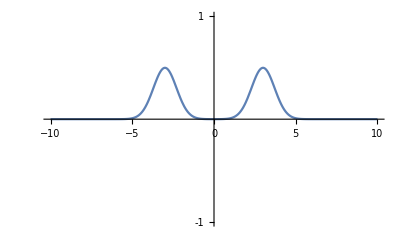

```mathematica
Plot[0.5*{ⅇ^(-(x-3)^2)-ⅇ^(-(x+3)^2)},{x,-10,10},Ticks->{{},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-1,1}]
Plot[0.5*{ⅇ^(-(x-3)^2)+ⅇ^(-(x+3)^2)},{x,-10,10},Ticks->{{},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-1,1}]
```

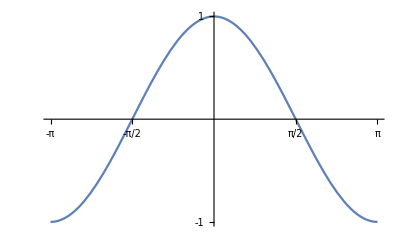

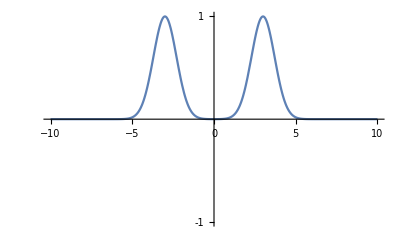

```mathematica
Plot[{Cos[x]},{x,-π,π},Ticks->{{-π,-π/2,π/2,π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{ⅇ^(-(x-3)^2)+ⅇ^(-(x+3)^2)},{x,-10,10},Ticks->{{},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-1,1}]
```

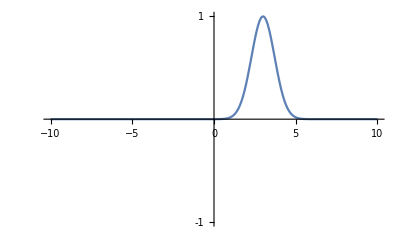

```mathematica
Plot[{ⅇ^(-(x-3)^2)},{x,-10,10},Ticks->{{},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-1,1}]
```

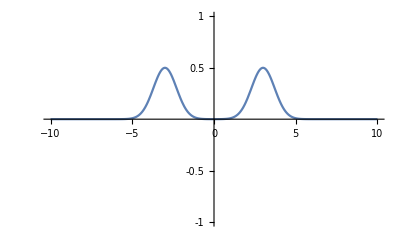

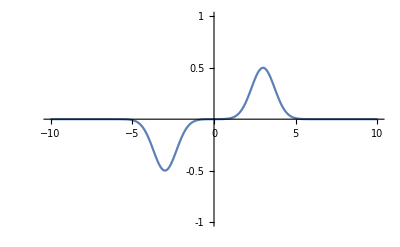

```mathematica
Plot[{0.5*(ⅇ^(-(x-3)^2)+ⅇ^(-(x+3)^2))},{x,-10,10},Ticks->{{},{-1,-0.5,1,0.5}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-1,1}]
Plot[{0.5*(ⅇ^(-(x-3)^2)-ⅇ^(-(x+3)^2))},{x,-10,10},Ticks->{{},{-1,-0.5,1,0.5}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-1,1}]
```

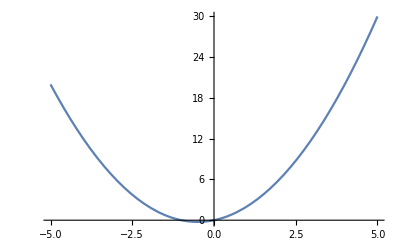

```mathematica
Plot[x*(1+x),{x,-5,5}]
```

```mathematica
∫_0^(2π) ⅇ^(ⅉ*2x)ⅆx
```

0

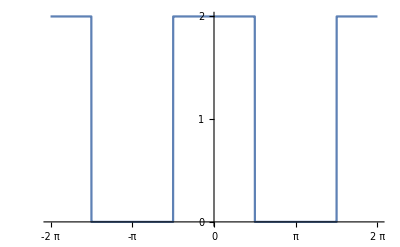

```mathematica
Plot[SquareWave[(x+π/2)/(2π)]+1,{x,-2π,2π},Ticks->{{-2π,-π,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
∫_0^(2π) Cos[0x]^2 ⅆx
```

2 π

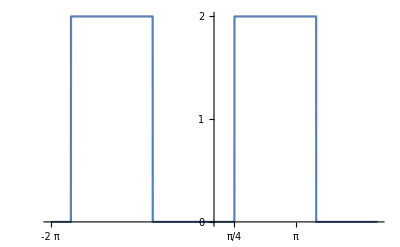

```mathematica
Plot[SquareWave[(x-π/4)/(2π)]+1,{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

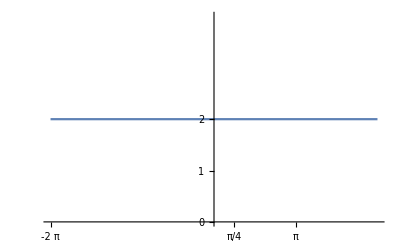

```mathematica
Plot[SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x+π/4)/(2π)]+1),{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

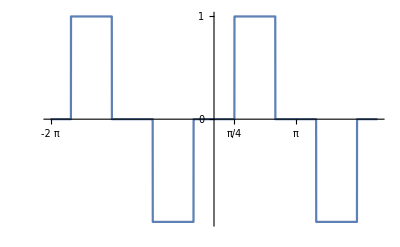

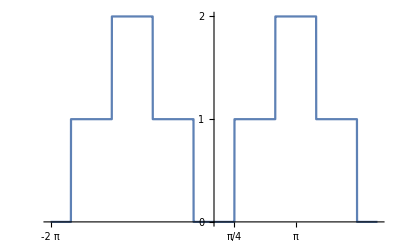

```mathematica
Plot[1/2*(SquareWave[(x-π/4)/(2π)]+1-(SquareWave[(-x-π/4)/(2π)]+1)),{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[1/2*(SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x-π/4)/(2π)]+1)),{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

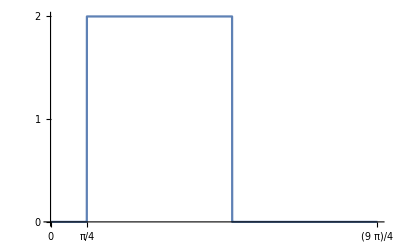

```mathematica
Plot[SquareWave[(x-π/4)/(2π)]+1,{x,0,2π+π/4},Ticks->{{0,π/4,2π+π/4},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
b2[n_]=Simplify[1/π∫_0^(2π) (1+SquareWave[(x-π/4)/(2π)])*Sin[n*x]ⅆx,Assumptions->n∈Integers]
a2[n_]=Simplify[1/π∫_0^(2π) (1+SquareWave[(x-π/4)/(2π)])*Cos[n*x]ⅆx,Assumptions->n∈Integers]
```

(2 (Cos[(n π)/4]-Cos[(5 n π)/4]))/(n π)

-(2 (Sin[(n π)/4]-Sin[(5 n π)/4]))/(n π)

```mathematica
sinSeries[n_,x_]:=∑_(i=1)^n Sin[i*x]*b2[i]
cosSeries[n_,x_]:=∑_(i=1)^n Cos[i*x]*a2[i]
```

```mathematica
c1[x_]=cosSeries[1,x];
c5[x_]=cosSeries[5,x];
c25[x_]=cosSeries[25,x];
s1[x_]=sinSeries[1,x];
s25[x_]=sinSeries[25,x];
s5[x_]=sinSeries[5,x];
```

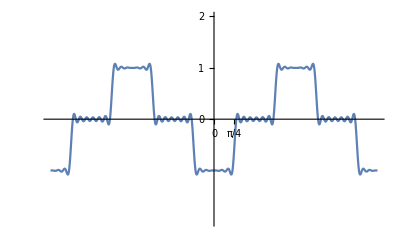

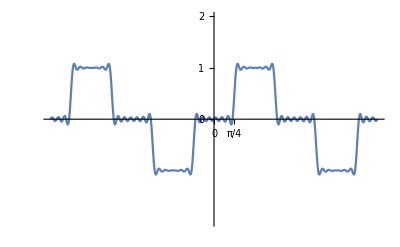

(8 (2 Cos[(n π)/4]+Cos[(3 n π)/4]) Sin[(n π)/4]^2)/(n π)

```mathematica
Plot[c25[x],{x,-2π,2π},Ticks->{{0,π/4,2π+π/4},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-2,2}]
Plot[s25[x],{x,-2π,2π},Ticks->{{0,π/4,2π+π/4},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None,PlotRange->{-2,2}]
```

```mathematica
∑_(n=1)^∞ b[n]*Sin[n*x]//Simplify
```

(ⅈ (-Log[1-ⅇ^(-ⅈ x)]+Log[1+ⅇ^(-ⅈ x)]+Log[1-ⅇ^(ⅈ x)]-Log[1+ⅇ^(ⅈ x)]))/π

```mathematica
test[n_]=Simplify[1/π∫_(π/4)^(9π/4) SquareWave[(x-π/4)/(2π)]*Sin[n*x]ⅆx,Assumptions->n∈Integers]
```

(Cos[(n π)/4]-2 Cos[(5 n π)/4]+Cos[(9 n π)/4])/(n π)

```mathematica
Table[test[n]-b2[n],{n,1,20}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
2*Cos[π/4]-2*Cos[5π/4]
```

2 √2

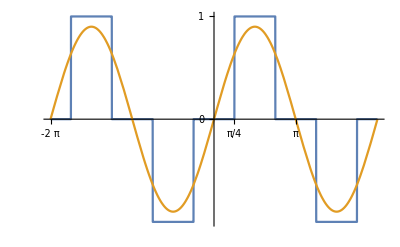

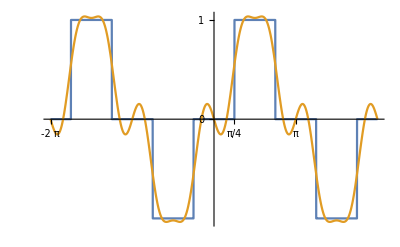

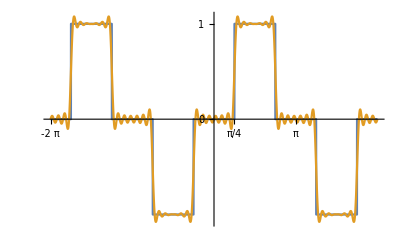

```mathematica
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1-(SquareWave[(-x-π/4)/(2π)]+1)),s1[x]},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1-(SquareWave[(-x-π/4)/(2π)]+1)),s5[x]},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1-(SquareWave[(-x-π/4)/(2π)]+1)),s25[x]},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
a2[n]
```

-(2 (Sin[(n π)/4]-Sin[(5 n π)/4]))/(n π)

```mathematica
Limit[a2[n],n->0]
```

2

```mathematica
b2[1]
```

(2 √2)/π

```mathematica
a2[n]
```

-(2 (Sin[(n π)/4]-Sin[(5 n π)/4]))/(n π)

```mathematica
test[n_]=-(4*Sin[(n π)/4])/(n π)
```

-(4 Sin[(n π)/4])/(n π)

```mathematica
Table[test[n]-a2[n],{n,1,10}]//Simplify
```

{0,-2/π,0,0,0,2/(3 π),0,0,0,-2/(5 π)}

```mathematica
a2[n]
```

-(2 (Sin[(n π)/4]-Sin[(5 n π)/4]))/(n π)

```mathematica
Limit[a[n],n->0]
```

2

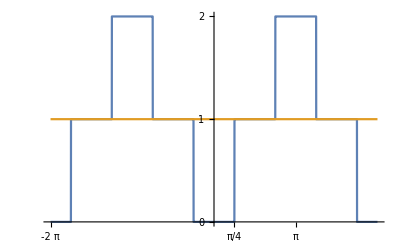

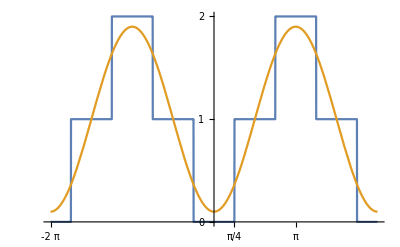

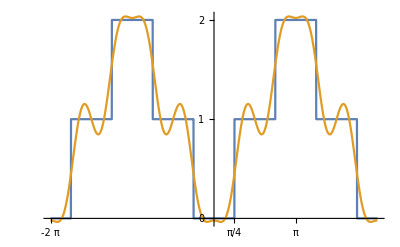

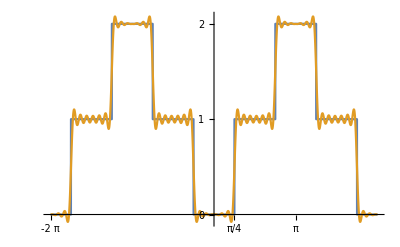

```mathematica
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x-π/4)/(2π)]+1)),1},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x-π/4)/(2π)]+1)),1+c1[x]},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x-π/4)/(2π)]+1)),1+c5[x]},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
Plot[{1/2*(SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x-π/4)/(2π)]+1)),1+c25[x]},{x,-2π,2π},Ticks->{{-2π,-π,π/4,0,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
1/(2π)∫_0^(2π) 1/2(SquareWave[(x-π/4)/(2π)]+1+(SquareWave[(-x-π/4)/(2π)]+1))ⅆx
```

1

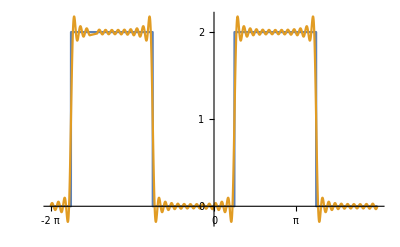

```mathematica
Plot[{(SquareWave[(x-π/4)/(2π)]+1),1+c25[x]+s25[x]},{x,-2π,2π},Ticks->{{-2π,-π,0,π/4,π,2π},{0,1,2}},TicksStyle->Directive["Label", 14],AxesLabel->{None, None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
1/(2π)∫_0^(2π) SquareWave[x/(2π)] ⅇ^(-ⅉ x)ⅆx
```

-(2 ⅈ)/π

```mathematica
1/(2π)∫_0^(2π) SquareWave[(x+π/2)/(2π)] ⅇ^(ⅉ x)ⅆx
```

2/π

```mathematica
c[n_]=Simplify[1/(2π)∫_-π^π SquareWave[(x+π/2)/(2π)] ⅇ^(-ⅉ n x)ⅆx,Assumptions->n∈Integers]//Simplify
```

(ⅈ (-1)^n (-1+ⅈ^n)^3 (1+ⅈ^n))/(2 n π)

```mathematica
(ⅈ (-1)^n (-1+ⅈ^n)^3 (1+ⅈ^n))/(2 n π)==2/(n π)Sin[(n π)/2]//Simplify
```

(ⅈ (-1)^n (-1+ⅈ^n)^3 (1+ⅈ^n)-4 Sin[(n π)/2])/(2 n π)==0

```mathematica
test[n_]=2/(n π)Sin[(n π)/2]
```

(2 Sin[(n π)/2])/(n π)

```mathematica
Table[test[n]-c[n]//Simplify,{n,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

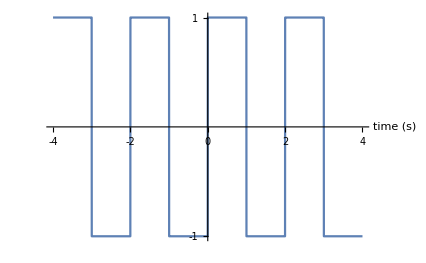

```mathematica
Plot[SquareWave[t/2],{t,-4,4},Ticks->{{-4,-2,0,2,4},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],Exclusions->None]
```

```mathematica
1/2∫_0^2 SquareWave[t/2]*ⅇ^(-ⅉ*(2π)/2*t)ⅆt
```

-(2 ⅈ)/π

```mathematica
∑_(n=-∞)^∞ Sinc[(n π)/2]*1/(1+ⅉ*ω0*n*τ)ⅇ^(ⅉ*ω0*n*t)//Simplify
```

1/π ⅇ^(-ⅈ t ω0) (-HurwitzLerchPhi[-ⅈ ⅇ^(-ⅈ t ω0),1,1+ⅈ/(τ ω0)]-HurwitzLerchPhi[ⅈ ⅇ^(-ⅈ t ω0),1,1+ⅈ/(τ ω0)]+ⅇ^(ⅈ t ω0) (π-ⅇ^(ⅈ t ω0) HurwitzLerchPhi[-ⅈ ⅇ^(ⅈ t ω0),1,1-ⅈ/(τ ω0)]-ⅇ^(ⅈ t ω0) HurwitzLerchPhi[ⅈ ⅇ^(ⅈ t ω0),1,1-ⅈ/(τ ω0)]+ⅈ Log[1-ⅈ ⅇ^(-ⅈ t ω0)]-ⅈ Log[1+ⅈ ⅇ^(-ⅈ t ω0)]+ⅈ Log[1-ⅈ ⅇ^(ⅈ t ω0)]-ⅈ Log[1+ⅈ ⅇ^(ⅈ t ω0)]))

```mathematica
cCircuit[n_]=1/(1+ⅉ*n)*test[n]
```

(2 Sin[(n π)/2])/((1+ⅈ n) n π)

```mathematica
circuitSeries
```

(ⅈ (-1)^n (-1+ⅈ^n)^3 (1+ⅈ^n))/(2 n π)